```mathematica
Quit[]
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
SetDirectory[NotebookDirectory[]];

enzModelsDir = "/home/mrama/Dropbox/MASSef/examples/"
mainDir=enzModelsDir<>"code_data/";
Import[mainDir<>"sim_plot_functions.m"];
Import[mainDir<>"simulation.m"];
```

/home/mrama/Dropbox/MASSef/examples/

## Build models

```mathematica
baseDir =enzModelsDir<> "FBP2/fit_FBP2/output/";
```

```mathematica
ssdThreshold=1;
baseModel=constructModel[{Overscript[fdp^c->f6p^c+pi^c, FBP2]}];
(*updateCustomRateLaws[baseModel, {Subscript[v, FBP2]->((FBP2^)_^ kcat_f_ fdp^c[t] (fdp^c[t]/S05_fdp_+(f6p^c[t] pi^c[t])/(S05_f6p_ S05_pi_))^(-1+nH_) (1-(f6p^c[t] pi^c[t])/(K_FBP2 fdp^c[t])))/(S05_fdp_ (1-2 (fdp^c[t]/S05_fdp_)^nH_+(f6p^c[t]/S05_f6p_+fdp^c[t]/S05_fdp_)^nH_+(fdp^c[t]/S05_fdp_+pi^c[t]/S05_pi_)^nH_+(fdp^c[t]/S05_fdp_+(f6p^c[t] pi^c[t])/(S05_f6p_ S05_pi_))^nH_))}];*)
```

```mathematica
updateCustomRateLaws[baseModel, {Subscript[v, FBP2]->((FBP2^)_^(  (kcat_f_ fdp^c[t])/S05_fdp_ -(kcat_r_  f6p^c[t] pi^c[t])/(S05_f6p_ S05_pi_)) (fdp^c[t]/S05_fdp_+(f6p^c[t] pi^c[t])/(S05_f6p_ S05_pi_))^(-1+nH_))/(S05_fdp_ (1-2 (fdp^c[t]/S05_fdp_)^nH_+(f6p^c[t]/S05_f6p_+fdp^c[t]/S05_fdp_)^nH_+(fdp^c[t]/S05_fdp_+pi^c[t]/S05_pi_)^nH_+(fdp^c[t]/S05_fdp_+(f6p^c[t] pi^c[t])/(S05_f6p_ S05_pi_))^nH_))}];
```

```mathematica
inputDir = baseDir<>"model_simulations/models/";
If[!DirectoryQ[inputDir],
	CreateDirectory[inputDir,CreateIntermediateDirectories-> True]
];


nModelEnsembles = 2;
Do[
eqParams = Import[baseDir <> "treated_data/predicted_params_distribution_p10_1000_"<>ToString@modelEnsembleI<>"_log_ssd_predS05.csv", "CSV"];

eMASSModelList=Import[baseDir<>"model_simulations/models/model_FBP2_all_1000_"<>ToString@modelEnsembleI<>".mx"];

modelList={};

Do[
If[eqParams[[modelI,1]]< ssdThreshold && modelI < (Length@eMASSModelList+3),

model = baseModel;

metInitialConc = FilterRules[eMASSModelList[[modelI-2]]["InitialConditions"],baseModel["Species"]];
metInitialConc=Map[Keys@# -> Values@#&, metInitialConc];
updateInitialConditions[model,metInitialConc];

paramList={ S05_fdp_-> eqParams[[modelI,2]],S05_f6p_->eqParams[[modelI,3]], S05_pi_->eqParams[[modelI,4]], nH_-> eqParams[[modelI,5]],  kcat_f_-> eqParams[[modelI,6]],kcat_r_-> eqParams[[modelI,7]],Underscript[K, FBP2]-> eqParams[[modelI,8]],  Underscript[Volume, c]-> 1, (FBP2^)_^->9.72*10^-8 };
updateParameters[model, paramList];

AppendTo[modelList,model],

Break[]],

{modelI, 3,Length@eqParams}]; 

Export[inputDir<>"model_FBP2_hill_rev_1000_"<>ToString@modelEnsembleI<>".mx",modelList, "MX"];,

{modelEnsembleI, 0, nModelEnsembles}];
```

## Hill simulations

```mathematica
getFirstHillModelData[modelI_, resWorking_, headerConcEnz_, headerConcMets_, headerFlux_, indEnz_, indMet_, tValues_]:=
	Block[{simConcEnz, simConcMets, simFlux},

	simConcMets=Join[{Flatten@{"t", headerConcMets}},
					Table[
						Flatten[{tVal, Flatten@{Values@{resWorking[[modelI, 1]][[indMet]]}} /. t-> tVal}], 
					{tVal,tValues}]];
		
	simFlux=Join[{Flatten@{"t", headerFlux}},
				Table[
					Flatten[{tVal, Flatten@{Values@resWorking[[modelI, 2]]} /. t-> tVal}], 
				{tVal,tValues}]];

	Return[{{}, simConcMets, simFlux}];
];
```

```mathematica
getHillModelData[modelI_, resWorking_, simConcEnz_, simConcMets_, simFlux_, headerConcEnz_, headerConcMets_, headerFlux_, indEnz_,  indMet_, tValues_]:=
	Block[{simConcEnzLocal, simConcMetsLocal, simFluxLocal, simConcEnzTemp, simConcMetsTemp, simFluxTemp},

						
	simConcMetsTemp=Join[{Flatten@{"t",headerConcMets}},
						Table[
							Flatten[{tVal, Flatten@{Values@{resWorking[[modelI, 1]][[indMet]]}}/.t-> tVal}],
						{tVal,tValues}]];
	
	simFluxTemp=Join[{Flatten@{"t",headerFlux}},
					Table[
						Flatten[{tVal,Flatten@{Values@resWorking[[modelI, 2]]}/.t-> tVal}],
					{tVal,tValues}]];
	
	
	simConcMetsLocal = MapThread[Flatten[{#1,#2}]&, {simConcMets,simConcMetsTemp}];
	simFluxLocal = MapThread[Flatten[{#1,#2}]&, {simFlux,simFluxTemp}];

	Return[{{},simConcMetsLocal, simFluxLocal}];
];
```

```mathematica
simulateHillEnsembleNoCheck[inputDir_, outputDir_, enzName_, modelID_, nModelEnsembles_, tFinal_, tValues_, 
				initCondList_, headerConcEnz_, headerConcMets_, headerFlux_, indEnz_, subInd_, prodInd_, KeqVal_:""]:=
	Block[{KeqData, prods, subs, indMet, modelList,
			metsList, res, resWorking, modelI, simConcEnz, simConcMets, simFlux, simConcEnzTemp, simConcMetsTemp, 
			simFluxTemp},
	 
	indMet = Flatten[{subInd, prodInd}];

	Do[

		modelList = Import[inputDir <> "model_" <> enzName <> "_" <> modelID <> "_" <> ToString[modelEnsembleI] <> ".mx"];
		Print[inputDir <> "model_" <> enzName <> "_" <> modelID <> "_" <> ToString[modelEnsembleI] <> ".mx"];
		res = Map[TimeConstrained[simulate[modelList[[#]], {t, 0, tFinal}, InitialConditions -> initCondList, MaxSteps-> Infinity], 30, "err"]&, Range[1, Length@modelList]];
		resWorking = Delete[res, Position[res,"err"]];	

		modelI=1;
				
		{simConcEnz, simConcMets, simFlux} = getFirstHillModelData[modelI, resWorking, headerConcEnz, headerConcMets, headerFlux, indEnz, indMet, tValues];
		
		Do[ (* go through individual models *)
			
				
			{simConcEnz, simConcMets, simFlux} = getHillModelData[modelI, resWorking, simConcEnz, simConcMets, 
							simFlux, headerConcEnz, headerConcMets, headerFlux, indEnz, indMet, tValues];,
	
		{modelI, 2, Length@resWorking}];

		Export[outputDir <> "/sim_res_conc_mets_"<>modelID<>"_"<>ToString[modelEnsembleI] <> "_" <>ToString[KeqVal] <> ".csv", simConcMets, "TSV"];
		Export[outputDir <> "/sim_res_flux_"<>modelID<>"_"<>ToString[modelEnsembleI] <> "_" <>ToString[KeqVal] <> ".csv", simFlux, "TSV"];

		Export[outputDir<> "/data_mx/sim_res_"<>modelID<>"_"<>ToString[modelEnsembleI] <> "_" <> ToString[KeqVal] <> ".mx", resWorking, "MX"];,

	{modelEnsembleI, nModelEnsembles[[1]], nModelEnsembles[[2]]}];
	
	
];
```

## Simulations

```mathematica
conc/.t-> tFinal
```

{f6p^c→0.0177194,fdp^c→3.94575×10^-7,pi^c→0.0390994}

```mathematica
(Times@@Values@FilterRules[conc/.t-> tFinal, {pi^c,f6p^c}])/Values@FilterRules[conc/.t-> tFinal, {fdp^c}]
```

{41.5}

```mathematica
modelList=Import[inputDir<>"model_FBP2_hill_3.mx"];
```

```mathematica
modelList=Delete[modelList,{{75},{80},{83}}];
```

```mathematica
modelList//Length
```

83

```mathematica
Do[
tFinal=5*10^12;
Print[modelI];
{conc,flux}=simulate[modelList[[modelI]],{t,0,tFinal}];,
{modelI, 1, Length@modelList}];
```

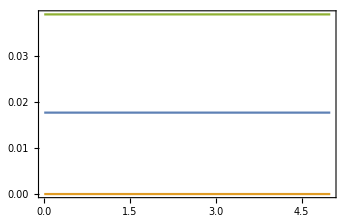

```mathematica
plotSimulation[conc,{t,0,tFinal}, PlotFunction-> Plot]
```

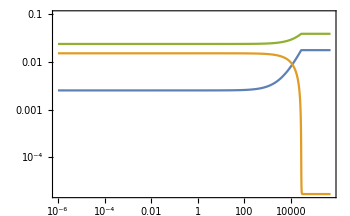

```mathematica
tFinal=5*10^5;
{conc,flux}=simulate[modelList[[9300]],{t,0,tFinal}];
plotSimulation[conc,{t,0,tFinal}, PlotRange-> {{0,tFinal},{0.,0.1}}]
```

```mathematica
modelList[[9300]]["Parameters"]
```

{S05_fdp_→0.0000696091,S05_f6p_→509107.,S05_pi_→0.781854,nH_→1.91334,kcat_FBP2→5.6992,K_FBP2→41.4844,Volume_c→1,(FBP2^)_^→9.72×10^-8}

### Systematic simulations

```mathematica
enzName="FBP2";

outputDirBase = baseDir<>"model_simulations/data/";
If[!DirectoryQ[outputDirBase],
	CreateDirectory[outputDirBase,CreateIntermediateDirectories-> True]
];



headerConcMets={"fdp","f6p",  "pi"};
headerFlux={"v_1"};
subInd = {2};
prodInd={1,3};
indEnz={};

initCondList={};
outputDirList={"noPerturb"};


tValues=Map[10^#&,Range[-6,3, 0.1]];
tFinal=1000;
tValues=Insert[tValues,0., 1];


modelIDList={"hill_rev_1000"};
nModelEnsembles={0,2};


outputDir =outputDirBase;
If[!DirectoryQ[outputDir<>"/data_mx/"],
	CreateDirectory[outputDir<>"/data_mx/",CreateIntermediateDirectories-> True]
];
```

```mathematica
headerConcEnz={};
```

```mathematica
Do[

simulateHillEnsembleNoCheck[inputDir, outputDir, enzName, modelID, nModelEnsembles, tFinal, tValues, initCondList, headerConcEnz, headerConcMets, headerFlux, indEnz,subInd, prodInd];,


{modelID, modelIDList}];
```

/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_hill_rev_1000_0.mx

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {15.8489} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_hill_rev_1000_1.mx

/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_hill_rev_1000_2.mx